```mathematica
ClearAll["Global`*"]
```

```mathematica
Dhyp[n_,k_,a_]:=Dhyp[n,k,a]=Sum[Binomial[k,j] Dhyp[n/(m^(k-j)),j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
Dhyp[n_,1,a_]:=Floor[n]-a+1;Dhyp[n_,0,a_]:=1
DA[n_,k_,a_]:=Sum[ DA[n/j,k-1,a],{j,a,n}];DA[n_,0,a_]:=1

da[n_,k_,c_]:=c Sum[ da[n/(j c),k-1,c],{j,1+1/c, n/c^k}];da[n_,0,c_]:=1
dc[n_,k_,c_]:=c^-k Dhyp[n c^k, k,c+1]
de[n_,k_,c_]:=c^-k DA[n c^k, k,c+1]

df[n_,k_,c_]:=c^-k Sum[ DA[n c^k j^-1,k-1,c+1],{j,c+1, n c^k}]
db[n_,k_,c_]:=c^-1 Sum[ db[n c^1 j^-1, k-1,c],      {j,c+1, n c^k}];db[n_,0,c_]:=1
dbb[n_,k_,c_]:=Sum[ dbb[n c^1 j^-1, k-1,c],      {j,c+1, n c^k}];dbb[n_,0,c_]:=1

$RecursionLimit=1000000
Dh[n_,k_,a_]:=Dh[n,k,a]=If[n<a^k,0,Sum[Binomial[k,j] Dh[n/a^j,k-j,a+1],{j,0,k}]];Dh[n_,0,a_]:=1
dhl[n_, k_, c_] := c^-k Dh[n c^k, k,c+1]
```

1000000

```mathematica
{db[nn=200,kk=2,cc=4],da[nn,kk,1/cc],dc[nn,kk,cc],de[nn,kk,cc],df[nn,kk,cc], dg[nn,kk,cc]}
```

{6513/8,6513/8,6513/8,6513/8,6513/8,328167/256}

```mathematica
di[n_, k_, c_]:=Sum[ (c^-1 db[n c^1 j^-1, k-1,c])-(c^-k  DA[n c^k j^-1,k-1,c+1]),{j,c+1, n c^k}]
```

```mathematica
di[200,3,4]
```

0

```mathematica
di2[n_, k_, c_,j_]:= (c^-1 db[n c^1 j^-1, k,c])-(c^-(k+1)  DA[n c^(k+1) j^-1,k,c+1])
```

```mathematica
di2[200,2,2,4]
```

0

```mathematica
di3[n_, k_, c_]:= (c^-1 db[n c^1 , k,c])-(c^-(k+1)  DA[n c^(k+1),k,c+1])
```

```mathematica
di3[120,3,2]
```

0

```mathematica
di4[n_, k_, c_]:= (db[n, k,c])-(c^-k  DA[n c^k,k,c+1])
```

```mathematica
di4[160,4,2]
```

0

```mathematica
di5[n_, k_, c_]:= (c^-2 db[n c^2 , k,c])-(c^-(k+2)  DA[n c^(k+2),k,c+1])
```

```mathematica
di5[60,3,2]
```

0

```mathematica
di6[n_, k_, c_,a_]:= (c^-a db[n c^a , k,c])-(c^-(k+a)  DA[n c^(k+a),k,c+1])
```

```mathematica
di6[160,3,2,-3]
```

0

```mathematica
di7[n_, k_, c_]:= (c^k db[n c^-k , k,c])- DA[n,k,c+1]
```

```mathematica
di7[160,3,2]
```

0

```mathematica
di8[n_, k_, c_]:= (c^k db[n c^-k , k,c])
```

```mathematica
di8[100,2,1]
```

283

```mathematica
di9[n_, k_, c_]:= ((c-1)^k db[n (c-1)^-k , k,(c-1)])
```

```mathematica
di9[100,2,2]
```

283

```mathematica
Dhyp[100,2,3]
```

186

```mathematica
N[4 Sum[ 1,{j,2,(100/4)},{k,2,((100)/(2 j))/2}]]
```

152.

```mathematica
di9[100,2,3]
```

186

```mathematica
4 db[100 /4 , 2,2]
```

186

```mathematica
db[100 , 2,1]
```

283

```mathematica
9 db[100 /9 , 2,3]
```

125

```mathematica
Dhyp[100,2,4]
```

125

```mathematica
db2[n_,c_]:=Sum[ 1,{j,1+c,n c^2},{k,1+c,(c n /j) c}]
```

```mathematica
db2[25,2]
```

186

```mathematica
db2[100/(3^2),3]
```

125

```mathematica
db2[100/(s^2),s]/.s->2
```

186

```mathematica
dbb[100 /9 , 2,3]
```

125

```mathematica
N[db[30,2,50]]
```

72.4572

```mathematica
N[Gamma[2,0,-Log[100]]/Gamma[2]]
```

361.517-4.41506×10^-14 ⅈ

1000000

1000000

```mathematica
N[dhl[100,2,30]]
```

358.271

```mathematica
dha[n_,k_,a_]:=Sum[(-1)^j Binomial[k,j] dha[n/(a-1)^j,k-j,a-1],{j,0,k}];dha[n_,0,a_]:=1
dha[n_,k_,2]:=d2[n,k]
dhla[n_, k_, c_] := c^-k dha[n c^k, k,c+1]
```

```mathematica
dha[n,2,5]
```

3-2 (-2+d2[n/4,1])-2 (-1+d2[n/3,1])-2 d2[n/2,1]+d2[n,2]

```mathematica
Table[{j,dhla[n,2,j]},{j,1,10}]//TableForm
```

1 | d2[n,2]
2 | 1/4 (1-2 d2[2 n,1]+d2[4 n,2])
3 | 1/9 (2-2 (-1+d2[3 n,1])-2 d2[(9 n)/2,1]+d2[9 n,2])
4 | 1/16 (3-2 (-2+d2[4 n,1])-2 (-1+d2[(16 n)/3,1])-2 d2[8 n,1]+d2[16 n,2])
5 | 1/25 (4-2 (-3+d2[5 n,1])-2 (-2+d2[(25 n)/4,1])-2 (-1+d2[(25 n)/3,1])-2 d2[(25 n)/2,1]+d2[25 n,2])
6 | 1/36 (5-2 (-4+d2[6 n,1])-2 (-3+d2[(36 n)/5,1])-2 (-2+d2[9 n,1])-2 (-1+d2[12 n,1])-2 d2[18 n,1]+d2[36 n,2])
7 | 1/49 (6-2 (-5+d2[7 n,1])-2 (-4+d2[(49 n)/6,1])-2 (-3+d2[(49 n)/5,1])-2 (-2+d2[(49 n)/4,1])-2 (-1+d2[(49 n)/3,1])-2 d2[(49 n)/2,1]+d2[49 n,2])
8 | 1/64 (7-2 (-6+d2[8 n,1])-2 (-5+d2[(64 n)/7,1])-2 (-4+d2[(32 n)/3,1])-2 (-3+d2[(64 n)/5,1])-2 (-2+d2[16 n,1])-2 (-1+d2[(64 n)/3,1])-2 d2[32 n,1]+d2[64 n,2])
9 | 1/81 (8-2 (-7+d2[9 n,1])-2 (-6+d2[(81 n)/8,1])-2 (-5+d2[(81 n)/7,1])-2 (-4+d2[(27 n)/2,1])-2 (-3+d2[(81 n)/5,1])-2 (-2+d2[(81 n)/4,1])-2 (-1+d2[27 n,1])-2 d2[(81 n)/2,1]+d2[81 n,2])
10 | 1/100 (9-2 (-8+d2[10 n,1])-2 (-7+d2[(100 n)/9,1])-2 (-6+d2[(25 n)/2,1])-2 (-5+d2[(100 n)/7,1])-2 (-4+d2[(50 n)/3,1])-2 (-3+d2[20 n,1])-2 (-2+d2[25 n,1])-2 (-1+d2[(100 n)/3,1])-2 d2[50 n,1]+d2[100 n,2])

```mathematica
dha1[n_,k_,a_]:=Sum[(-1)^j Binomial[k,j] dha1[n/(a-1)^j,k-j,a-1],{j,0,k}];dha1[n_,0,a_]:=1
dha1[n_,k_,1]:=d1[n,k]
dhla1[n_, k_, c_] := c^-k dha1[n c^k, k,c+1]
```

```mathematica
Table[{j,Expand[dhla1[n,2,j]]},{j,1,10}]//TableForm
```

1 | 1-2 d1[n,1]+d1[n,2]
2 | 1-1/2 d1[2 n,1]-1/2 d1[4 n,1]+1/4 d1[4 n,2]
3 | 1-2/9 d1[3 n,1]-2/9 d1[(9 n)/2,1]-2/9 d1[9 n,1]+1/9 d1[9 n,2]
4 | 1-1/8 d1[4 n,1]-1/8 d1[(16 n)/3,1]-1/8 d1[8 n,1]-1/8 d1[16 n,1]+1/16 d1[16 n,2]
5 | 1-2/25 d1[5 n,1]-2/25 d1[(25 n)/4,1]-2/25 d1[(25 n)/3,1]-2/25 d1[(25 n)/2,1]-2/25 d1[25 n,1]+1/25 d1[25 n,2]
6 | 1-1/18 d1[6 n,1]-1/18 d1[(36 n)/5,1]-1/18 d1[9 n,1]-1/18 d1[12 n,1]-1/18 d1[18 n,1]-1/18 d1[36 n,1]+1/36 d1[36 n,2]
7 | 1-2/49 d1[7 n,1]-2/49 d1[(49 n)/6,1]-2/49 d1[(49 n)/5,1]-2/49 d1[(49 n)/4,1]-2/49 d1[(49 n)/3,1]-2/49 d1[(49 n)/2,1]-2/49 d1[49 n,1]+1/49 d1[49 n,2]
8 | 1-1/32 d1[8 n,1]-1/32 d1[(64 n)/7,1]-1/32 d1[(32 n)/3,1]-1/32 d1[(64 n)/5,1]-1/32 d1[16 n,1]-1/32 d1[(64 n)/3,1]-1/32 d1[32 n,1]-1/32 d1[64 n,1]+1/64 d1[64 n,2]
9 | 1-2/81 d1[9 n,1]-2/81 d1[(81 n)/8,1]-2/81 d1[(81 n)/7,1]-2/81 d1[(27 n)/2,1]-2/81 d1[(81 n)/5,1]-2/81 d1[(81 n)/4,1]-2/81 d1[27 n,1]-2/81 d1[(81 n)/2,1]-2/81 d1[81 n,1]+1/81 d1[81 n,2]
10 | 1-1/50 d1[10 n,1]-1/50 d1[(100 n)/9,1]-1/50 d1[(25 n)/2,1]-1/50 d1[(100 n)/7,1]-1/50 d1[(50 n)/3,1]-1/50 d1[20 n,1]-1/50 d1[25 n,1]-1/50 d1[(100 n)/3,1]-1/50 d1[50 n,1]-1/50 d1[100 n,1]+1/100 d1[100 n,2]

```mathematica
dha1a[n_,k_,a_]:=Sum[(-1)^j Binomial[k,j] dha1a[n/(a-1)^j,k-j,a-1],{j,0,k}];dha1a[n_,0,a_]:=1
dha1a[n_,k_,1]:=Dhyp[n,k,1]
dhla1a[n_, k_, c_] := c^-k dha1a[n c^k, k,c+1]
```

```mathematica
N[dhla1a[100,2,4]]
```

338.625

```mathematica
-N[Gamma[3,0,-Log[100]]/Gamma[3]]
```

698.863-1.71417×10^-13 ⅈ

```mathematica
$RecursionLimit=1000000
Dh[n_,k_,a_]:=Dh[n,k,a]=If[n<a^k,0,Sum[Binomial[k,j] Dh[n/a^j,k-j,a+1],{j,0,k}]];Dh[n_,0,a_]:=1
dhl[n_, k_, c_] := c^-k Dh[n c^k, k,c+1]
```

```mathematica
N[Dh[100,2,4]]
```

125.

```mathematica
DH1[n_,k_,a_]:=Sum[(-1)^j Binomial[k,j]Dh[n/((a-1)^j),k-j,a-1],{j,0,k}]
```

```mathematica
DH1[100,2,5]
```

82

```mathematica
Dhyp[100,2,5]
```

82

```mathematica
ap[n_, c_] := c^-2 ( Dhyp[ c^2 n, 2,1] -2 Sum[ Dhyp[c^2 n j^-1,1,1]-j+1,{j,1,c}]+c )
ap2[n_, c_] := c^-2 ( d1[ c^2 n, 2] -2 Sum[ d1[c^2 n j^-1,1]-j+1,{j,1,c}]+c )
ap3[n_, c_] := c^-2 ( d1[ c^2 n, 2] -2 Sum[ d1[c^2 n j^-1,1],{j,1,c}]+c^2 )
```

```mathematica
N[ap[100,4]]
```

338.625

```mathematica
d11[n_,k_]:=Dhyp[n,k,1]
N[1/16 (4-2 (-3+d1[4 n,1])-2 (-2+d1[(16 n)/3,1])-2 (-1+d1[8 n,1])-2 d1[16 n,1]+d1[16 n,2])/.{d1->d11,n->100}]
```

338.625

```mathematica
Expand[ap2[100,10]]
```

1-1/50 d1[1000,1]-1/50 d1[10000/9,1]-1/50 d1[1250,1]-1/50 d1[10000/7,1]-1/50 d1[5000/3,1]-1/50 d1[2000,1]-1/50 d1[2500,1]-1/50 d1[10000/3,1]-1/50 d1[5000,1]-1/50 d1[10000,1]+1/100 d1[10000,2]

```mathematica
Expand[1/16 (4-2 (-3+d1[4 n,1])-2 (-2+d1[(16 n)/3,1])-2 (-1+d1[8 n,1])-2 d1[16 n,1]+d1[16 n,2])/.{n->100}]
```

1-1/8 d1[400,1]-1/8 d1[1600/3,1]-1/8 d1[800,1]-1/8 d1[1600,1]+1/16 d1[1600,2]

```mathematica
Expand[ap3[100,4]]
```

1-1/8 d1[400,1]-1/8 d1[1600/3,1]-1/8 d1[800,1]-1/8 d1[1600,1]+1/16 d1[1600,2]

```mathematica
N[ap[100,100]]
```

```mathematica
360.5354
```

```mathematica
ap4[n_, c_] := c^-2 ( Dhyp[ c^2 n, 2,1])-2 c^-2 Sum[ Dhyp[c^2 n j^-1,1,1],{j,1,c}]+1
```

```mathematica
N[ap4[100,10]]
```

351.92

```mathematica
ap5[n_, c_] := c^-2 ( Dhyp[ c^2 n, 2,1])-2 c^-2 Sum[ Floor[c^2 n j^-1],{j,1,c}]+1
```

```mathematica
N[ap5[100^2,60]]
```

81938.3

```mathematica
N[Gamma[2,0,-2Log[100]]/Gamma[2]]
```

82104.4-1.00548×10^-11 ⅈ

```mathematica
dha[n_,k_,a_]:=Sum[(-1)^j Binomial[k,j] dha[n/(a-1)^j,k-j,a-1],{j,0,k}];dha[n_,0,a_]:=1
dha[n_,k_,2]:=d2[n,k]
dhla[n_, k_, c_] := c^-k dha[n c^k, k,c+1]
```

```mathematica
Table[{j,Expand[dhla[n,2,j]]},{j,1,10}]//TableForm
```

1 | d2[n,2]
2 | 1/4-1/2 d2[2 n,1]+1/4 d2[4 n,2]
3 | 4/9-2/9 d2[3 n,1]-2/9 d2[(9 n)/2,1]+1/9 d2[9 n,2]
4 | 9/16-1/8 d2[4 n,1]-1/8 d2[(16 n)/3,1]-1/8 d2[8 n,1]+1/16 d2[16 n,2]
5 | 16/25-2/25 d2[5 n,1]-2/25 d2[(25 n)/4,1]-2/25 d2[(25 n)/3,1]-2/25 d2[(25 n)/2,1]+1/25 d2[25 n,2]
6 | 25/36-1/18 d2[6 n,1]-1/18 d2[(36 n)/5,1]-1/18 d2[9 n,1]-1/18 d2[12 n,1]-1/18 d2[18 n,1]+1/36 d2[36 n,2]
7 | 36/49-2/49 d2[7 n,1]-2/49 d2[(49 n)/6,1]-2/49 d2[(49 n)/5,1]-2/49 d2[(49 n)/4,1]-2/49 d2[(49 n)/3,1]-2/49 d2[(49 n)/2,1]+1/49 d2[49 n,2]
8 | 49/64-1/32 d2[8 n,1]-1/32 d2[(64 n)/7,1]-1/32 d2[(32 n)/3,1]-1/32 d2[(64 n)/5,1]-1/32 d2[16 n,1]-1/32 d2[(64 n)/3,1]-1/32 d2[32 n,1]+1/64 d2[64 n,2]
9 | 64/81-2/81 d2[9 n,1]-2/81 d2[(81 n)/8,1]-2/81 d2[(81 n)/7,1]-2/81 d2[(27 n)/2,1]-2/81 d2[(81 n)/5,1]-2/81 d2[(81 n)/4,1]-2/81 d2[27 n,1]-2/81 d2[(81 n)/2,1]+1/81 d2[81 n,2]
10 | 81/100-1/50 d2[10 n,1]-1/50 d2[(100 n)/9,1]-1/50 d2[(25 n)/2,1]-1/50 d2[(100 n)/7,1]-1/50 d2[(50 n)/3,1]-1/50 d2[20 n,1]-1/50 d2[25 n,1]-1/50 d2[(100 n)/3,1]-1/50 d2[50 n,1]+1/100 d2[100 n,2]

```mathematica
a2p[n_, c_] := c^-2 ( Dhyp[ c^2 n, 2,2] -2 Sum[ Dhyp[c^2 n j^-1,1,2],{j,2,c}] )+(c-1)^2/c^2
```

```mathematica
N[a2p[100,30]]
```

358.271

```mathematica
Table[{j,Expand[dhla[n,3,j]]},{j,1,10}]//TableForm
```

1 | d2[n,3]
2 | -1/8+3/8 d2[2 n,1]-3/8 d2[4 n,2]+1/8 d2[8 n,3]
3 | -8/27+1/9 d2[3 n,1]+2/9 d2[(9 n)/2,1]+1/9 d2[(27 n)/4,1]-1/9 d2[9 n,2]-1/9 d2[(27 n)/2,2]+1/27 d2[27 n,3]
4 | -27/64+3/64 d2[4 n,1]+3/32 d2[(16 n)/3,1]+3/64 d2[(64 n)/9,1]+3/32 d2[8 n,1]+3/32 d2[(32 n)/3,1]+3/64 d2[16 n,1]-3/64 d2[16 n,2]-3/64 d2[(64 n)/3,2]-3/64 d2[32 n,2]+1/64 d2[64 n,3]
5 | -64/125+3/125 d2[5 n,1]+6/125 d2[(25 n)/4,1]+3/125 d2[(125 n)/16,1]+6/125 d2[(25 n)/3,1]+6/125 d2[(125 n)/12,1]+6/125 d2[(25 n)/2,1]+3/125 d2[(125 n)/9,1]+6/125 d2[(125 n)/8,1]+6/125 d2[(125 n)/6,1]-3/125 d2[25 n,2]+3/125 d2[(125 n)/4,1]-3/125 d2[(125 n)/4,2]-3/125 d2[(125 n)/3,2]-3/125 d2[(125 n)/2,2]+1/125 d2[125 n,3]
6 | -125/216+1/72 d2[6 n,1]+1/36 d2[(36 n)/5,1]+1/72 d2[(216 n)/25,1]+1/36 d2[9 n,1]+1/36 d2[(54 n)/5,1]+1/36 d2[12 n,1]+1/72 d2[(27 n)/2,1]+1/36 d2[(72 n)/5,1]+1/18 d2[18 n,1]+1/36 d2[(108 n)/5,1]+1/72 d2[24 n,1]+1/36 d2[27 n,1]+1/36 d2[36 n,1]-1/72 d2[36 n,2]-1/72 d2[(216 n)/5,2]+1/72 d2[54 n,1]-1/72 d2[54 n,2]-1/72 d2[72 n,2]-1/72 d2[108 n,2]+1/216 d2[216 n,3]
7 | -216/343+3/343 d2[7 n,1]+6/343 d2[(49 n)/6,1]+3/343 d2[(343 n)/36,1]+6/343 d2[(49 n)/5,1]+6/343 d2[(343 n)/30,1]+6/343 d2[(49 n)/4,1]+3/343 d2[(343 n)/25,1]+6/343 d2[(343 n)/24,1]+6/343 d2[(49 n)/3,1]+6/343 d2[(343 n)/20,1]+6/343 d2[(343 n)/18,1]+3/343 d2[(343 n)/16,1]+6/343 d2[(343 n)/15,1]+6/343 d2[(49 n)/2,1]+12/343 d2[(343 n)/12,1]+6/343 d2[(343 n)/10,1]+3/343 d2[(343 n)/9,1]+6/343 d2[(343 n)/8,1]-3/343 d2[49 n,2]+6/343 d2[(343 n)/6,1]-3/343 d2[(343 n)/6,2]-3/343 d2[(343 n)/5,2]+3/343 d2[(343 n)/4,1]-3/343 d2[(343 n)/4,2]-3/343 d2[(343 n)/3,2]-3/343 d2[(343 n)/2,2]+1/343 d2[343 n,3]
8 | -343/512+3/512 d2[8 n,1]+3/256 d2[(64 n)/7,1]+3/512 d2[(512 n)/49,1]+3/256 d2[(32 n)/3,1]+3/256 d2[(256 n)/21,1]+3/256 d2[(64 n)/5,1]+3/512 d2[(128 n)/9,1]+3/256 d2[(512 n)/35,1]+3/256 d2[16 n,1]+3/256 d2[(256 n)/15,1]+3/256 d2[(128 n)/7,1]+3/512 d2[(512 n)/25,1]+3/128 d2[(64 n)/3,1]+3/256 d2[(512 n)/21,1]+3/256 d2[(128 n)/5,1]+3/256 d2[(256 n)/9,1]+9/512 d2[32 n,1]+3/256 d2[(512 n)/15,1]+3/256 d2[(256 n)/7,1]+3/128 d2[(128 n)/3,1]+3/256 d2[(256 n)/5,1]+3/512 d2[(512 n)/9,1]+3/256 d2[64 n,1]-3/512 d2[64 n,2]-3/512 d2[(512 n)/7,2]+3/256 d2[(256 n)/3,1]-3/512 d2[(256 n)/3,2]-3/512 d2[(512 n)/5,2]+3/512 d2[128 n,1]-3/512 d2[128 n,2]-3/512 d2[(512 n)/3,2]-3/512 d2[256 n,2]+1/512 d2[512 n,3]
9 | -512/729+1/243 d2[9 n,1]+2/243 d2[(81 n)/8,1]+1/243 d2[(729 n)/64,1]+2/243 d2[(81 n)/7,1]+2/243 d2[(729 n)/56,1]+2/243 d2[(27 n)/2,1]+1/243 d2[(729 n)/49,1]+2/243 d2[(243 n)/16,1]+2/243 d2[(81 n)/5,1]+2/243 d2[(243 n)/14,1]+2/243 d2[(729 n)/40,1]+1/81 d2[(81 n)/4,1]+2/243 d2[(729 n)/35,1]+2/243 d2[(729 n)/32,1]+2/243 d2[(243 n)/10,1]+2/243 d2[(729 n)/28,1]+2/243 d2[27 n,1]+1/243 d2[(729 n)/25,1]+4/243 d2[(243 n)/8,1]+2/243 d2[(243 n)/7,1]+2/243 d2[(729 n)/20,1]+4/243 d2[(81 n)/2,1]+1/81 d2[(729 n)/16,1]+2/243 d2[(243 n)/5,1]+2/243 d2[(729 n)/14,1]+4/243 d2[(243 n)/4,1]+2/243 d2[(729 n)/10,1]+1/243 d2[81 n,1]-1/243 d2[81 n,2]+2/243 d2[(729 n)/8,1]-1/243 d2[(729 n)/8,2]-1/243 d2[(729 n)/7,2]+2/243 d2[(243 n)/2,1]-1/243 d2[(243 n)/2,2]-1/243 d2[(729 n)/5,2]+1/243 d2[(729 n)/4,1]-1/243 d2[(729 n)/4,2]-1/243 d2[243 n,2]-1/243 d2[(729 n)/2,2]+1/729 d2[729 n,3]
10 | -729/1000+(3 d2[10 n,1])/1000+3/500 d2[(100 n)/9,1]+(3 d2[(1000 n)/81,1])/1000+3/500 d2[(25 n)/2,1]+3/500 d2[(125 n)/9,1]+3/500 d2[(100 n)/7,1]+(3 d2[(125 n)/8,1])/1000+3/500 d2[(1000 n)/63,1]+3/500 d2[(50 n)/3,1]+3/500 d2[(125 n)/7,1]+3/500 d2[(500 n)/27,1]+3/500 d2[20 n,1]+(3 d2[(1000 n)/49,1])/1000+3/500 d2[(125 n)/6,1]+3/500 d2[(200 n)/9,1]+3/500 d2[(500 n)/21,1]+3/250 d2[25 n,1]+(9 d2[(250 n)/9,1])/1000+3/500 d2[(200 n)/7,1]+3/500 d2[(125 n)/4,1]+3/250 d2[(100 n)/3,1]+3/500 d2[(250 n)/7,1]+3/500 d2[(1000 n)/27,1]+(3 d2[40 n,1])/1000+3/250 d2[(125 n)/3,1]+3/500 d2[(1000 n)/21,1]+3/250 d2[50 n,1]+3/250 d2[(500 n)/9,1]+(9 d2[(125 n)/2,1])/1000+3/500 d2[(200 n)/3,1]+3/500 d2[(500 n)/7,1]+3/250 d2[(250 n)/3,1]+3/500 d2[100 n,1]-(3 d2[100 n,2])/1000+(3 d2[(1000 n)/9,1])/1000-(3 d2[(1000 n)/9,2])/1000+3/500 d2[125 n,1]-(3 d2[125 n,2])/1000-(3 d2[(1000 n)/7,2])/1000+3/500 d2[(500 n)/3,1]-(3 d2[(500 n)/3,2])/1000-(3 d2[200 n,2])/1000+(3 d2[250 n,1])/1000-(3 d2[250 n,2])/1000-(3 d2[(1000 n)/3,2])/1000-(3 d2[500 n,2])/1000+d2[1000 n,3]/1000

```mathematica
Sum[1,{j,2,c},{k,2,c}]
```

(-1+c)^2

```mathematica
Sum[ 1, {j,2,10},{k,2,((10^2) 100)/j}]/.{c->10, n->100}
```

19279

```mathematica
Sum[ 1, {j,2,c},{k,2,((c^2) n)/j}]/.{c->10, n->100}
```

1214683/63

```mathematica
Sum[ 1, {j,2,(c^2 n) / (c n)},{k,2,(c^2) n/j}]/.{c->10, n->100}
```

1214683/63

```mathematica
Sum[ 1, {k,2,(10^2) 100},{j,2,10}]
```

89991

```mathematica
f1[n_, c_]:=Sum[ 1, {j,2,(c^2 n) / (c n)},{k,2,(c^2) n / j}]
f2[n_, c_]:=Sum[ 1, {k,2,(c^2) n},{j,2,(c^2 n) / (c n)/k}]
```

```mathematica
f1[100,10]
```

19279

```mathematica
f2[100,10]
```

8

```mathematica
a3p[n_, c_] := c^-3 ( Sum[1,{j,2,c^3 n},{k,2,c^3 n/j},{m,2,c^3 n/(j k)}]-3Sum[1,{j,2,c},{k,2,c^3 n/j},{m,2,c^3 n/(j k)}]+3Sum[1,{j,2,c},{k,2,c},{m,2,c^3 n/(j k)}]-Sum[1,{j,2,c},{k,2,c},{m,2,c}])
```

```mathematica
N[a3p[100,20]]
```

672.244

```mathematica
Dhyp[100,3,2]
```

324

```mathematica
N[-Gamma[3,0,-Log[100]]/Gamma[3]]
```

698.863-1.71417×10^-13 ⅈ

```mathematica
a13p[n_, c_] := c^-3 ( Sum[1,{j,1,c^3 n},{k,1,c^3 n/j},{m,1,c^3 n/(j k)}]-3Sum[1,{j,1,c},{k,1,c^3 n/j},{m,1,c^3 n/(j k)}]+3Sum[1,{j,1,c},{k,1,c},{m,1,c^3 n/(j k)}]-Sum[1,{j,1,c},{k,1,c},{m,1,c}])
```

```mathematica
N[a13p[100,10]]
```

646.722

```mathematica
a1kp[n_, c_,r_] := c^-3 ( Sum[1,{j,r,c^3 n},{k,r,c^3 n/j},{m,r,c^3 n/(j k)}]-3Sum[1,{j,r,c},{k,r,c^3 n/j},{m,r,c^3 n/(j k)}]+3Sum[1,{j,r,c},{k,r,c},{m,r,c^3 n/(j k)}]-Sum[1,{j,r,c},{k,r,c},{m,r,c}])
```

```mathematica
N[a1kp[100,20,10]]
```

672.244

```mathematica
N[a1kp[100,20,7]]
```

672.244

```mathematica
aa1kp[n_, c_,r_] := c^-3 ( Sum[1,{j,r,c^3 n},{k,r,c^3 n/j},{m,r,c^3 n/(j k)}]-Sum[1,{j,r,c},{k,r,c},{m,r,c}])
```

```mathematica
N[aa1kp[100,20,1]]
```

10279.8

```mathematica
Limit[ (x-1)^2/x^2,{x->Infinity}]
```

{1}

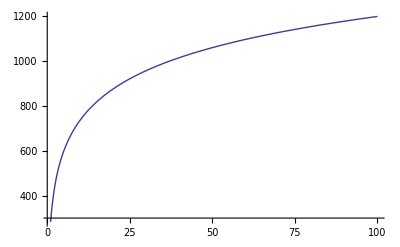

```mathematica
Plot[ Dhyp[100 c^2,2,2]/c^2,{c,1,100}]
```

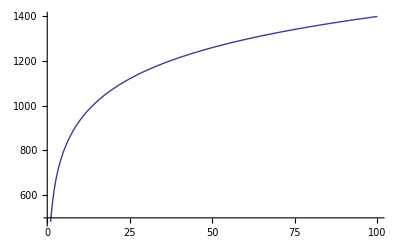

```mathematica
Plot[ Dhyp[100 c^2,2,1]/c^2,{c,1,100}]
```

```mathematica
Limit[c^-3 ( Sum[1,{j,1,c^3 n},{k,1,c^3 n/j},{m,1,c^3 n/(j k)}]-3Sum[1,{j,1,c},{k,1,c^3 n/j},{m,1,c^3 n/(j k)}]+3Sum[1,{j,1,c},{k,1,c},{m,1,c^3 n/(j k)}]-Sum[1,{j,1,c},{k,1,c},{m,1,c}]),{c->Infinity}]
```

$Aborted

```mathematica
Table[{j,Expand[dhla[n,1,j]]},{j,1,10}]//TableForm
```

1 | d2[n,1]
2 | -1/2+1/2 d2[2 n,1]
3 | -2/3+1/3 d2[3 n,1]
4 | -3/4+1/4 d2[4 n,1]
5 | -4/5+1/5 d2[5 n,1]
6 | -5/6+1/6 d2[6 n,1]
7 | -6/7+1/7 d2[7 n,1]
8 | -7/8+1/8 d2[8 n,1]
9 | -8/9+1/9 d2[9 n,1]
10 | -9/10+1/10 d2[10 n,1]